# Bifurcación de tridente subcrítica

## Forma normal 1:

### Espacio fase

```mathematica
Manipulate[Plot[r*x+x^3,{x,-2,2},AxesLabel->{x,OverDot[x]},PlotRange->{{-2,2},{-8,8}}],{r,-4,4}]
```

### Diagrama de bifurcación

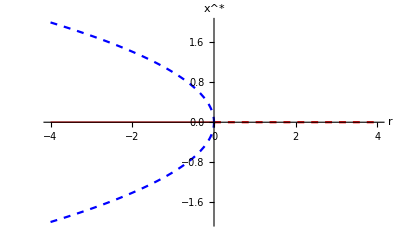

```mathematica
bdsub=Show[Plot[0,{r,-4,0},AxesLabel->{r,SuperStar[x]},PlotStyle->{Red,Thick},PlotRange->{{-4,4},{-2,2}}],Plot[0,{r,0,4},AxesLabel->{r,SuperStar[x]},PlotStyle->{Red,Dashed},PlotRange->{{-4,4},{-2,2}}],Plot[Sqrt[-r],{r,-4,0},AxesLabel->{r,SuperStar[x]},PlotStyle->{Blue,Dashed},PlotRange->{{-4,4},{-2,2}}],Plot[-Sqrt[-r],{r,-4,0},AxesLabel->{r,SuperStar[x]},PlotStyle->{Blue,Dashed},PlotRange->{{-4,4},{-2,2}}]]
```

## Forma normal 2:

### Espacio fase

```mathematica
Manipulate[Plot[r*x+x^3-x^5,{x,-1.5,1.5},AxesLabel->{x,OverDot[x]},PlotRange->{{-1.5,1.5},{-0.2,0.2}}],{r,-1,1}]
```

### Diagrama de bifurcación

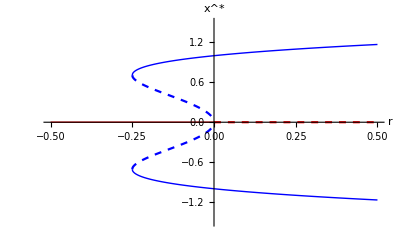

```mathematica
bdsubext=Show[Plot[0,{r,-1/2,0},AxesLabel->{r,SuperStar[x]},PlotStyle->{Red,Thick},PlotRange->{{-1/2,1/2},{-3/2,3/2}}],Plot[0,{r,0,1/2},AxesLabel->{r,SuperStar[x]},PlotStyle->{Red,Dashed},PlotRange->{{-1/2,1/2},{-3/2,3/2}}],ListPlot[sols11,AxesLabel->{r,SuperStar[x]},PlotStyle->{Blue,Thick},Joined->True,PlotRange->{{-1/2,1/2},{-3/2,3/2}}],ListPlot[sols21,AxesLabel->{r,SuperStar[x]},PlotStyle->{Blue,Thick},Joined->True,PlotRange->{{-1/2,1/2},{-3/2,3/2}}],ListPlot[sols12,AxesLabel->{r,SuperStar[x]},PlotStyle->{Blue,Dashed},Joined->True,PlotRange->{{-1/2,1/2},{-3/2,3/2}}],ListPlot[sols22,AxesLabel->{r,SuperStar[x]},PlotStyle->{Blue,Dashed},Joined->True,PlotRange->{{-1/2,1/2},{-3/2,3/2}}]]
```